## AMO Physics Notebook Author: Huan Q. Bui Massachusetts Institute of Technology First updated: Jan 30, 2023 Last updated: Feb 01, 2023

### List of Constants (SI units)

General Physics Constants

```mathematica
cSOL=2.99792458*10^8; (*m/s*)
```

```mathematica
hbar=1.05457182*10^(-34); (*J s*)
```

```mathematica
ϵ0=8.8541878128*10^(-12);(*F/m*)
```

```mathematica
e=1.60217663*10^(-19);(*Coulombs*)
```

```mathematica
mE=9.1093837*10^(-31);(*kg*)
```

```mathematica
μB=e*hbar/(2*mE);(*Bohr magneton in Joules per Tesla*)
```

```mathematica
μBFreq = hbar*2*Pi*1.399624604; (*MHz/G*)
```

```mathematica
γE=e/mE; (*electron gyromagnetic ratio*)
```

Can also write γ_E=-g_sμ_B/ℏ, where g_s=2 from Dirac theory.

```mathematica
μE=γE*S; (*Here S = ℏ/2, the electron's spin angular momentum*)
```

```mathematica
α=e^2/(4*Pi*ϵ0*hbar*cSOL); (*Fine-structure constant ~ 1/137*)
```

g-factors:

```mathematica
gL=0.99999587;(*electron L=1 orbital g-factor*)
```

```mathematica
gS=2.0023193043737; (*electron spin g-factor*)
```

```mathematica
gF[F_,II_,J_,gJ_,gI_]:=gJ*( (F*(F+1)-II*(II+1) +J*(J+1)) /(2*F*(F+1)))+gI*(  (F*(F+1)+II*(II+1)-J*(J+1)) /(2*F*(F+1)));
```

Lithium-6 Constants

```mathematica
mLi6=9.9883414*10^(-27); (*kg*)
```

```mathematica
λLi6D2=670.977338*10^(-9); (*m*)
```

```mathematica
ωLi6D2=2*Pi*446.799677*10^(12);(*Hz*)
```

```mathematica
ΓLi6D2=5.8724*10^6; (*MHz -- angular frequency *)
```

```mathematica
vRecoilLi6D2=0.09886776 ;(*m/s*)
```

```mathematica
TRecoilLi6D2=3.53581152*10^(-6); (*Kelvin*)
```

Lithium-6 g-factors:

```mathematica
gILi6=-0.0004476540; (*total nuclear g-factor*)
```

```mathematica
gJLi6S12=2.0023010; (*gJ for 2 Subscript[S, 1/2]*)
```

```mathematica
gJLi6P12=0.6668; (*gJ for 2 Subscript[P, 1/2]*)
```

```mathematica
gJLi6P32=1.335; (*gJ for 2 Subscript[P, 3/2]*)
```

Sodium-23 Constants

```mathematica
mNa23=0.381754035*10^(-25); (*kg*)
```

```mathematica
λNa23D2=589.1583264*10^(-9);(*m*)
```

```mathematica
ωNa23D2=2*Pi*508.8487162*10^(12);(*Hz*)
```

```mathematica
ΓNa23D2=2*Pi*9.7946*10^6;(*Hz*)
```

```mathematica
vRecoilNa23D2=0.029461; (*m/s*)
```

```mathematica
TRecoilNa23D2=2.3998*10^(-6); (*Kelvin*)
```

Sodium-23 g-factors:

```mathematica
gINa23=0;
```

```mathematica
gJNa23S12=0;
```

```mathematica
gJNa23P12=0;
```

```mathematica
gJNa23P32=0;
```

### Two-Level System: Resonance

The Hamiltonian of a Quantized Spin-1/2 in a Rotating Magnetic Field

Rapid Adiabatic Passage: Landau-Zener Crossing

### Early Atomic Physics

### The Hydrogen Atom

### The Alkalis

### Spin-Orbit Coupling

### Hyperfine Structure

### Interaction of Atoms with Radiations

Two-level system (Rabi problem)

Readily observed in radio-frequency (RF) spectroscopy for e.g . transitions between Zeeman or hf levels . These transitions also have negligible spontaneous emission, so n most cases the atoms evolve coherently .

Population in excited state: non-perturbative solution

```mathematica
Ω=1 ;(*Rabi frequency*)
```

```mathematica
P2[t_,δ_]:=(Ω^2/(Ω^2+δ^2))*Sin[Sqrt[Ω^2+δ^2]*t/2]^2
```

```mathematica
Manipulate[Plot[P2[t,δ],{δ,-3,3},PlotRange->{0,1}],{t,0,6*Pi/Ω}]
```

Bloch vector, Bloch sphere, and the Optical Bloch Equations

A pure quantum state ψ = (c1, c2) could be represented by a density matrix ρ. On the other hand, a quantum state on the Bloch sphere is specified by three coordinates (u,v,w). What is the correspondence between (u,v,w) and the density matrix ρ?  One can show that the density matrix corresponding to the state (u,v,w) is given by

Bloch vector

```mathematica
BlochVector[u_,v_,w_]:={u,v,w}
```

Density matrix - Bloch sphere correspondence

```mathematica
ρBloch[u_,v_,w_]:=(IdentityMatrix[2]+u*PauliMatrix[1]+v*PauliMatrix[2]+w*PauliMatrix[3])/2;
```

```mathematica
ρBloch[u,v,w]//MatrixForm
```

((1+w)/2 | 1/2 (u-ⅈ v)
1/2 (u+ⅈ v) | (1-w)/2)

With this, we can show that given a density matrix {{ρ11, ρ12}, {ρ21, ρ22}} where ρ12 = ρ21* then 

u = ρ_12 + ρ_21
v = - ⅈ (ρ_12 - ρ_21)
w = 1 - ρ_22

Evolution of Bloch vector: Optical Bloch equations without damping

The Bloch vector for the ideal two-level system and its evolution is entirely dictated by the Rabi frequency ωR and the detuning δ. Without damping, the evolution of the state vector is given by:

```mathematica
DBlochVectorDt[u_,v_,w_]:={δ*v, -δ*u+ωR*w,-ωR*v}
```

```mathematica
DBlochVectorDt[u,v,w]//MatrixForm
```

(v δ
-u δ+w ωR
-v ωR)

The magnitude of the Bloch vector for a pure state is constant

The Bloch vector is perpendicular to its time derivative. This implies that its magnitude is constantly unity. This means that the Bloch vector corresponds to the position vector of points on the surface of a sphere of unit radius -- the Bloch sphere.

```mathematica
Dot[BlochVector[u,v,w],DBlochVectorDt[u,v,w]]//FullSimplify
```

0

Look at the form of the time derivative of the Bloch vector, it has the form dB/dt = B x W where “x” is the cross product and W is the vector:

```mathematica
W[ωR_,δ_]:={ωR,0,δ}
```

```mathematica
W[ωR,δ]//MatrixForm
```

(ωR
0
δ)

The Bloch vector precesses around the vector W with rate equal to the length of W. The evolution of the BLoch vector is similar to that of a magnetic moment in a magnetic field, where the magnetic moment precesses around the magnetic field.

Bloch sphere

```mathematica
BlochSphere = Graphics3D[{Opacity[0.2],Sphere[],Black,Opacity[1.],
PointSize[.02],Point[{0,0,0}],Point[{1,0,0}],Point[{-1,0,0}],Point[{0,1,0}],Point[{0,-1,0}],Point[{0,0,1}],Point[{0,0,-1}],
Line[{{0,1,0},{0,-1,0}}],
Line[{{0,0,1},{0,0,-1}}],
Line[{{1,0,0},{-1,0,0}}],
Text[Style[Row[{"|0⟩=",MatrixForm[{1,0}]}], 10], {0,0,1.3 }],
Text[Style[Row[{"|1⟩=",MatrixForm[{0,1}]}], 10], {0,0,-1.3 }],
Text[Style[Row[{"|R⟩"}], 10], {0,1.3 ,0}],
Text[Style[Row[{"|L⟩"}], 10],{0,-1.3 ,0}],
Text[Style[Row[{"|+⟩"}], 10], {1.6 ,-0.25,0}],
Text[Style[Row[{"|-⟩"}],10],{-1.5 ,0.3,0}]}];
```

```mathematica
Append[BlochSphere, Boxed->False]
```

-Graphics3D-

Ramsey Fringes

Driven Damped Lorentz Oscillator

Driven damped Lorentz oscillator

Optical Bloch equations with damping

In order to get the damped version of the optical Bloch equations, we simply add damping terms to each of du/dt, dv/dt, and dw/dt. Since u, v are terms related to coherences and w is related to the population in the excited state, the damping factor is -Γ/2 for u, v and -Γ for w.

Optical Bloch Equations with Damping

The Optical Bloch equations with damping are

```mathematica
DBlochVectorDtWithDamping[u_,v_,w_]:={δ*v-(Γ/2)*u, -δ*u+ωR*w-(Γ/2)*v,-ωR*v-Γ*(w-1)};
```

```mathematica
DBlochVectorDtWithDamping[u,v,w]//MatrixForm
```

(-(u Γ)/2+v δ
-(v Γ)/2-u δ+w ωR
-((-1+w) Γ)-v ωR)

Steady-state solution for the Optical Bloch equations

We typically don’t care about the transient solutions to the Optical Bloch equations because the timescales are often not relevant. Rather, the steady-state solution is much more relevant to us:

```mathematica
BlochSteadyState[ωR_,δ_,Γ_]:=(1/(δ^2+ωR^2/2+Γ^2/4))*{ωR*δ, ωR*Γ/2,δ^2+Γ^2/4}
```

Steady-state population of excited state

The steady-state population of the excited state is related to w via w = 1 - 2 ρ_22. So,

```mathematica
ρ22SteadyState[ωR_,δ_,Γ_]:= (1-Dot[BlochSteadyState[ωR,δ,Γ],{0,0,1}])/2//FullSimplify
```

```mathematica
ρ22SteadyState[ωR,δ,Γ]
```

ωR^2/(Γ^2+4 δ^2+2 ωR^2)

Notice that for very strong drive, i.e. the Rabi frequency ωR becomes large relative to the damping and detuning, the excited state population saturates to 1/2:

```mathematica
Limit[ρ22SteadyState[ωR,δ,Γ],{ωR->Infinity}]
```

1/2

The Optical Absorption Cross-section

Consider a sample of N atoms with thickness Δz. Light with intensity I(w,z) along the z-axis with frequency is incident on the sample. The attenuation of the light is modeled by an exponential decay:

dI(ω,z)/dz = - N σ(ω) I(ω,z) = - (N_1- N_2) σ(ω) I(ω,z)

Here N_1are the absorbing atoms and N_2are the emitting atoms (due to stimulated emission). By conservation of energy, the light attenuated per unit volume is the same as the amount of light that the atoms scatter out of the beams due to spontaneous emission. So, we have an equation:

(N_1 - N_2) σ(ω) I(ω) = N_2 ℏω Γ

Now, since we know w = (N_1 - N_2)/N and ρ_22= N_2/N, we can substitute in these quantities into the equation above and solve for the cross section σ(ω):

w(ω,δ,Γ) σ(ω) I(ω) = ρ_22(ω,δ,Γ) ℏω Γ

```mathematica
Solve[Dot[BlochSteadyState[ωR,δ,Γ],{0,0,1}]*σ*Intensity==ρ22SteadyState[ωR,δ,Γ]*ℏ*ω*Γ,σ]//FullSimplify
```

{{σ→(Γ ω ωR^2 ℏ)/(Intensity Γ^2+4 Intensity δ^2)}}

Okay, but notice that the absorption cross-section should not depend on the intensity of the light used. To see this, recall that the intensity of the light field is proportional to only the magnitude of the electric field squared. Moreover, there is a ωR^2 term in the denominator for σ, which is also proportional to the electric field magnitude squared. 

This means that we can cancel the electric field magnitude. After some manipulations, the absorption cross-section is dependent only on ω, ω_0, and Γ and takes the form:

σ(ω) ~ Γ/ω0^2 * Lorentzian(ω, Γ) ~  (1/ω0^2) *  Γ^2 / (δ^2 + Γ^2/4)

where the Lorentzian(ω, Γ) = gH(ω) is the lineshape function (Cauchy distribution). Here, “H” denotes homogeneous.

```mathematica
gH[ω_,ω0_,Γ_]:=(1/(2*Pi))*Γ/((ω - ω0)^2 + Γ^2/4);
```

```mathematica
σ[ω_,ω0_,Γ_]:=(3*(Pi^2*c^2)/ω0^2)*Γ*gH[ω,ω0,Γ];
```

```mathematica
σ[ω,ω0,Γ]
```

(3 c^2 π Γ^2)/(2 (Γ^2/4+(ω-ω0)^2) ω0^2)

Note the factor of 3 in the equation above. In a more general case, this factor can take values between 0 and 3, as it is given by g_2/g_1the ratio of the degeneracy levels. For alkali atoms, the D2 transition is s-p, and the ratio is indeed 3.

Resonance absorption cross section

The absorption cross-section peaks on resonance:

```mathematica
σ0=σ[ω0,ω0,Γ]
```

(6 c^2 π)/ω0^2

which is proportional to the square of the wavelength of the transition:

```mathematica
σ0/.{ω0->2Pi*c/λ0}
```

(3 λ0^2)/(2 π)

One thing to note from this is that the cross-section of atoms in photon-atom interaction can be much larger than the size of the atom. One could say that the “collisions” between atoms and photons have a large resonant enhancement.

Saturation Intensity

In order to quantity the amount of saturation, we return to the equation:

(N_1 - N_2) σ(ω) I(ω) = N_2 ℏω Γ

which after calling σ(ω) I(ω)/ℏω Γ = r and assuming N_1+N_2=N=1, we have

(N_1 - N_2) r = N_2  ------> N_2/N_1= r / (r+1) 

Solving for N_2 using N_1+N_2 = N = 1 gives

```mathematica
Solve[N2/(1-N2)==r/(r+1),N2]//FullSimplify
```

{{N2→r/(1+2 r)}}

We define the saturation parameter as 

s = I(ω)/I_sat(ω)=2r=2σ(ω) I(ω)/ℏωΓ  = I(ω) * (2σ(ω)/ℏωΓ)

```mathematica
s[ω_]:=Intensity[ω]*(2σ[ω,ω0,Γ])/(ℏ*ω*Γ)
```

From here, one can define the saturation intensity as a function of the frequency of the driving field:

```mathematica
ISat[ω_,ω0_,Γ_]:=ℏ*ω*Γ/(2*σ[ω,ω0,Γ])
```

The saturation intensity is minimized on resonance. This value is often referred to as the saturation intensity:

```mathematica
ISatMin=ISat[ω0,ω0,Γ]/.{ω0->2*Pi*c/λ0}
```

(2 c π^2 Γ ℏ)/(3 λ0^3)

Alternatively, we could also define the saturation intensity from the steady-state solution of the Bloch equations. Knowing that

N_1-N_2=1/(1+2r)=w

we obtain another definition of the saturation parameter in terms of the Rabi frequency and linewidth of the transition: 

s = 2r=I/I_sat=2Ω^2/Γ^2

```mathematica
s=2*ωR^2/Γ^2
```

(2 ωR^2)/Γ^2

Power Broadening

Suppose we are doing absorption imaging of atoms. What we observe is actually the attenuation of the imaging light due to the atoms. What we measure is proportional to the quantity w*σ(ω), which has the form:

```mathematica
wSS=1/(1+s*Γ^2/(Γ^2+4 (ω-ω0)^2));
```

```mathematica
σPowerBroadening[ω_,ω0_,Γ_,σ0_]:=σ0*Γ^2/(Γ^2+4 (ω-ω0)^2);
```

where in the definition for w in steady state we have used s = I/I_sat with I_sat being the saturation intensity, and rewriting I(ω)/I_sat(ω) as I(ω)/[ I_sat*σ0/σ(ω) ]. With these, we get:

```mathematica
wSS*σPowerBroadening[ω,ω0,Γ,σ0]//FullSimplify
```

(Γ^2 σ0)/((1+s) Γ^2+4 (ω-ω0)^2)

which is a Lorentzian with full-width at half-maximum:

```mathematica
ΔwFWHM=Γ*Sqrt[1+s];
```

We see that the lineshape is broadened as the light intensity approaches and exceeds the saturation intensity I_sat. This is call power broadening.

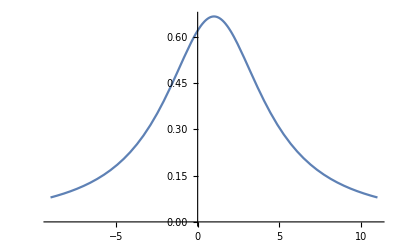

```mathematica
Plot[wSS*σPowerBroadening[ω,1,6,1]/.{s->0.5,Γ->6,ω0->1},{ω,-10+1,10+1}]
```

Doppler Broadening

AC-Stark Effect and Light Shift

In the rotation frame and time-dependent perturbation theory, the Hamiltonian in the presence of an oscillatory driving field is given by

```mathematica
HACStark[δ_,ωR_]:=(1/2)*{{δ,ωR},{ωR,-δ}};
```

```mathematica
HACStark[δ,ωR]//MatrixForm
```

(δ/2 | ωR/2
ωR/2 | -δ/2)

The eigenvalues are:

```mathematica
Eigenvalues[HACStark[δ,ωR]]
```

{-1/2 √(δ^2+ωR^2),1/2 √(δ^2+ωR^2)}

For ωR = 0, the energies are the same as those for the unperturbed system where the levels are spaced by δ. 

Normally, light shifts are important in regimes where the detuning is large (δ  >> ωR). In this case, we can do a Taylor series expansion of the eigenvalues to get the light shifts in the high-detuning regime:

The lower level’s energy is shifted by  - ωR^2 / 4δ

```mathematica
FullSimplify[Series[Eigenvalues[HACStark[δ,ωR]][[1]],{ωR,0,2}],δ>0]
```

-δ/2-ωR^2/(4 δ)+O[ωR]^3

whereas the higher level’s energy is shifted by + ωR^2 / 4δ

```mathematica
FullSimplify[Series[Eigenvalues[HACStark[δ,ωR]][[2]],{ωR,0,2}],δ>0]
```

δ/2+ωR^2/(4 δ)+O[ωR]^3

Notice that the light shift is proportional to the square of the Rabi frequency, so it is proportional to the light intensity. The light shift is also inversely proportional to the detuning. It is also dependent on the sign of the detuning, which is important for optical dipole trapping.

DC Stark Effect

DC Stark Effect for a Diatomic Molecule

Oscillator Strength

Selection Rules

### Doppler-Free Spectroscopy

### Laser Cooling and Trapping

Common Cooling Limits

### Optical Trapping

### Magnetic Trapping

### Evaporative Cooling

### Statistical Mechanics

### Bose-Einstein Condensation

### Degenerate Fermi Gas

### Feshbach Resonance

### Quantitative Analysis of Density Distributions

Trapped Atomic Gases

Fitting Functions for trapped and expanded Fermi gases

Absorption Imaging

Polarization Rotation Imaging

### Miscellaneous Calculations

```mathematica
Imbalance[TopB_, TopA_]:=(TopB-TopA)/(TopB+TopA);
```

```mathematica
N[Imbalance[368,85]]
```

0.624724